# stirap animation

## functions

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"\\images\\"}]];
```

```mathematica
BuildSchroedingerSystem[H_,psi0_,t0_:0]:=Module[
{hamiltonian=H,ψ0=psi0,ψ,statelength,eqs,ics,sys,P,i},
statelength = Length[ψ0];
ψ = Array[Subscript[P, #][t]&,statelength];
eqs = {};(*system to solve*)
ics = {};(*initial conditions*)
For[i=1,i<statelength+1,i++,
AppendTo[eqs,D[ψ[[i]],t]==-ⅈ (hamiltonian.ψ)[[i]]];
AppendTo[ics,(ψ[[i]]/.t->t0)==ψ0[[i]]];
];
sys = Flatten@Join[eqs,ics];
{ψ,sys}
];

(*R is the angular momentum bector which experiences the torque vector γ*)
TorqueVectorSphere[Rx_,Ry_,Rz_,γx_,γy_,γz_]:=Graphics3D[{{Specularity[Pink,5],Opacity[0.1],Sphere[]},{Red,Thick,Arrow[{{0,0,0},{Rx,Ry,Rz}}]},{Blue,Thick,Dashed,Line[{{0,0,0},{Rx,Ry,0}}]},
{Blue,Thick,Dashed,Line[{{Rx,Ry,0},{Rx,Ry,Rz}}]},{Green,Thick,Dashed,Line[{{0,0,0},{0,0,Rz}}]},
{Green,Thick,Dashed,Line[{{0,0,Rz},{Rx,Ry,Rz}}]},
{Purple,Thick,Arrow[{{0,0,0},{γx,γy,γz}}]},
Text[Style["3",20],{0,0,1.3}],Text[Style["1",20],{1.3,0,0}],Text[Style["2",20],{0,1.3,0}]},Boxed->False,Axes->True,AxesOrigin->{0,0,0},ImageSize->Medium];
```

## simulation

STIRAP

```mathematica
w=1.5;
μ=2.5;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
psi = {c1,c2,c3};
ⅈ H.psi//MatrixForm
```

(3 ⅈ c2 ⅇ^(-0.222222 (-1.25+t)^2) π
ⅈ (3 c1 ⅇ^(-0.222222 (-1.25+t)^2) π+3 c3 ⅇ^(-0.222222 (1.25+t)^2) π)
3 ⅈ c2 ⅇ^(-0.222222 (1.25+t)^2) π)

Time to run sim: 0 mins

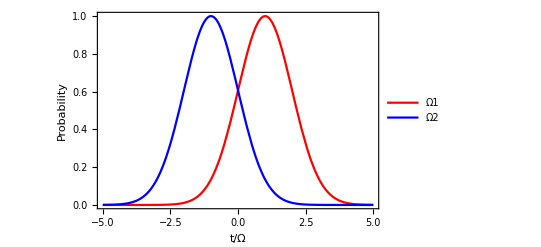

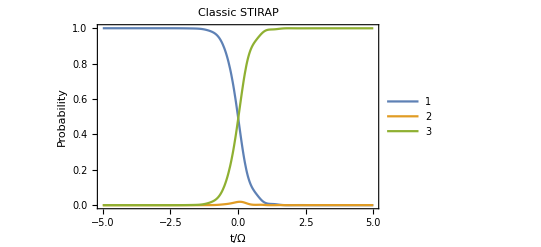

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Counter-intuitive pulse sequence*)
w=1;
μ=2;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Classic STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["counter_intuitive1.gif",gif]*)
```

counter_intuitive1.gif

Time to run sim: 0 mins

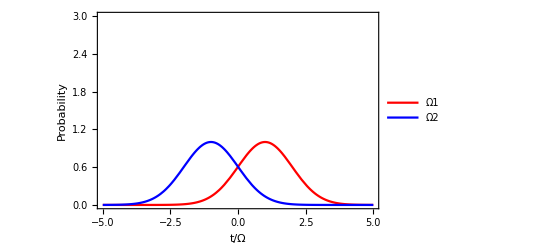

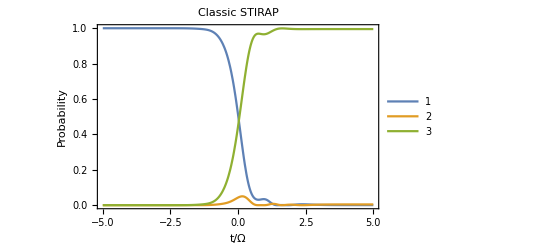

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Counter-intuitive pulse sequence*)
w=1;
μ=2;
Ω0=4π;
Ω1[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->{0,3},PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Classic STIRAP"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["counter_intuitive2.gif",gif]*)
```

counter_intuitive2.gif

Time to run sim: 0 mins

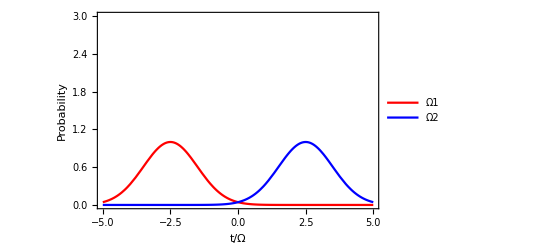

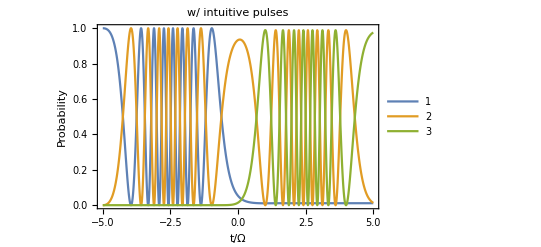

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Intuitive pulse sequence*)
w=1;
μ=5;
Ω0=6π;
Ω1[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->{0,3},PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["w/ intuitive pulses"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["intuitive1.gif",gif]*)
```

intuitive1.gif

Time to run sim: 0 mins

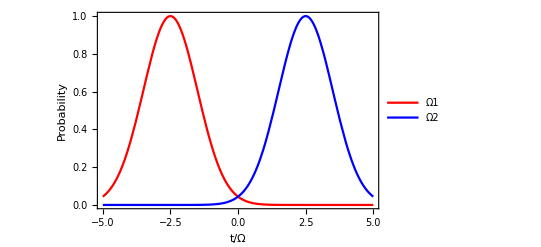

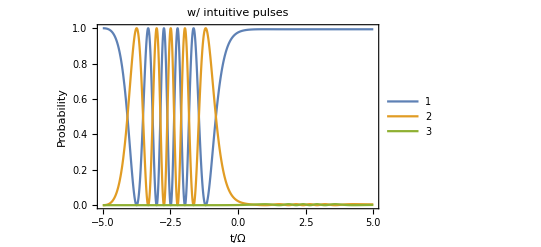

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {5.} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Intuitive pulse sequence*)
w=1;
μ=5;
Ω0=4π;
Ω1[t_]:=Ω0 Exp[(-(t+μ/2)^2)/(2 w^2)];
Ω2[t_]:=Ω0 Exp[(-(t-μ/2)^2)/(2 w^2)];
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ={1,0,0};(*start with atom in ground state*)
tmax=5;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,-tmax];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,-tmax,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,-tmax,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,-tmax,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["w/ intuitive pulses"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.001} ]
```

```mathematica
(*gif =Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,Ω1[t]/Ω0]/.t-> τ,{τ,-tmax,tmax,0.2}];
Export["intuitive2.gif",gif]*)
```

intuitive2.gif

```mathematica
i
```

4

```mathematica
Clear[t]
```

Raman

Time to run sim: 0 mins

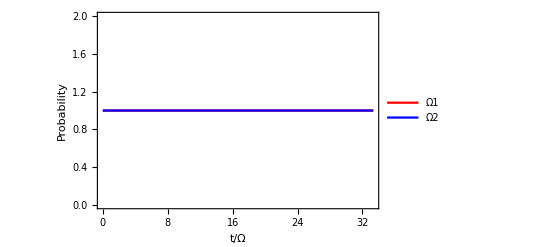

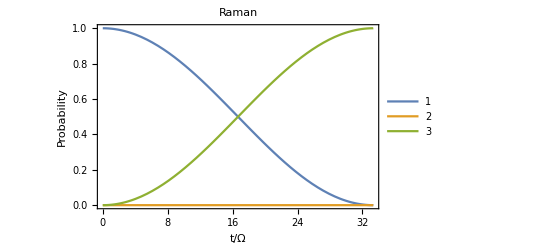

```mathematica
(*Raman pulse sequence*)
Ω0=6π;
Ω1[t_]:=Ω0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 100Ω0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={1,0,0};(*start with atom in ground state*)
Ωeff = Ω1[0]Ω2[0]/(2Δ1);
tmax=π/Ωeff;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Raman"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[Abs[soln[[1]]],Abs[soln[[2]]], Abs[ soln[[3]]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.1} ]
```

Time to run sim: 0 mins

-Graphics-

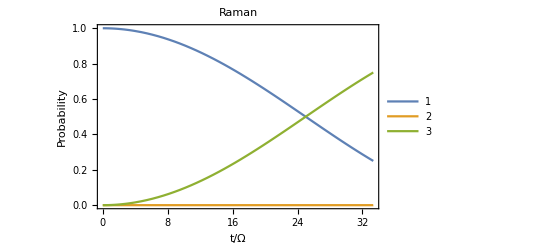

```mathematica
(*Raman pulse sequence*)
Ω0=4π;
Ω1[t_]:=Ω0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 100Ω0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={1,0,0};(*start with atom in ground state*)
Ωeff = Ω1[0]Ω2[0]/(2Δ1);
(*tmax=π/Ωeff;*)
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["Raman"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[Abs[soln[[1]]],Abs[soln[[2]]], Abs[ soln[[3]]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.1} ]
```

## misc graphics

Time to run sim: 0 mins

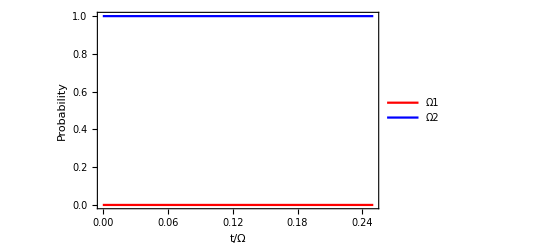

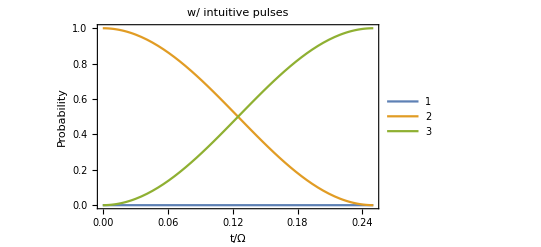

Part::partd: Part specification soln⟦1⟧ is longer than depth of object.

Part::partd: Part specification soln⟦2⟧ is longer than depth of object.

Part::partd: Part specification soln⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
(*Intuitive pulse sequence*)
w=1;
μ=5;
Ω0=4π;
Ω1[t_]:=0 ;
Ω2[t_]:=Ω0 ;
Δ1 = Δ2 = 0;
H=({{0, Ω1[t]/2, 0}, {Ω1[t]/2, Δ1, Ω2[t]/2}, {0, Ω2[t]/2, Δ1-Δ2}});
ψ0={0,-ⅈ,0};(*start with atom in ground state*)
tmax=π/Ω0;
{ψ,sys}=BuildSchroedingerSystem[H,ψ0,0];
{time,soln}= Timing[First@NDSolve[sys, ψ, {t,0,tmax}]];
Print[StringForm["Time to run sim: `` mins",Floor[time/60//N]]];
soln = Table[soln[[i,2]],{i,Range[Length[soln]]}];
Plot[{Ω1[t]/Ω0,Ω2[t]/Ω0},{t,0,tmax},PlotLegends->{"Ω1","Ω2"},LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All,PlotStyle->{Red,Blue}]
leg = {"1","2","3"};
plt=Plot[{Abs[soln[[1]]]^2,Abs[soln[[2]]]^2,Abs[soln[[3]]]^2},{t,0,tmax},PlotLegends->leg,PlotLabel-> Style[StringForm["w/ intuitive pulses"],Black,FontSize->14],LabelStyle->Directive[Black,FontSize->12],Axes-> False,Frame-> {True,True,False,False},FrameLabel->{"t/Ω","Probability"},PlotRange->All]

Manipulate[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,0.001} ]
```

```mathematica
plt=Show[Table[TorqueVectorSphere[soln[[1]],ⅈ soln[[2]],soln[[3]],Ω2[t]/Ω0,0,-Ω1[t]/Ω0]/.t-> τ,{τ,0,tmax,tmax/10} ],ImageResolution-> 400]
```

-Graphics3D-

```mathematica
Export[]
```

## algebra

Pulse area. just √(Ω_1^2+Ω_2^2), integrated over +- infinity?

```mathematica
Integrate[Exp[(-(t-μ/2)^2)/(2 w^2)]Exp[(-(t+μ/2)^2)/(2 w^2)]
```

```mathematica
Exp[(-(t-μ/2)^2)/(2 w^2)]Exp[(-(t+μ/2)^2)/(2 w^2)]//Simplify
```

ⅇ^(-(4 t^2+μ^2)/(4 w^2))

```mathematica
ⅇ^(-μ^2/(4 w^2))ⅇ^(-t^2/w^2)
```

Calculate the derivative of R in the torque picture

```mathematica
Clear[ϕ,θ,R,Γ,Ω1,Ω2,Δ1,Δ2]
R={c1,c2,c3};
Γ={Ω2,0,-Ω1};
Cross[Γ,R]
```

{c2 Ω1,-c1 Ω1-c3 Ω2,c2 Ω2}

```mathematica
H=({{0, Ω1/2, 0}, {Ω1/2, Δ1, Ω2/2}, {0, Ω2/2, Δ1+Δ2}})
```

{{0,Ω1/2,0},{Ω1/2,Δ1,Ω2/2},{0,Ω2/2,Δ1+Δ2}}

```mathematica
Assuming[Ω1∈Reals&&Ω2∈Reals&&Δ1∈Reals&&Δ2∈Reals,Eigensystem[H]]//FullSimplify
```

{{1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1],1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2],1/2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]},{{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]),1},{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]),1},{(Ω1 (1-(2 (Δ1+Δ2))/Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]))/Ω2,1/Ω2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]),1}}}

```mathematica
FullSimplify[#/√(#.#),Assumptions->{Ω1∈Reals,Ω2∈Reals}]&/@Eigensystem[H][[2]]
```

{{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,1]^2)))},{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,2]^2)))},{(Ω1 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]))/(Ω2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3] √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2))),(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])/(Ω2 √(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2))),1/(√(1+1/Ω2^2(-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2+(Ω1^2 (-2 (Δ1+Δ2)+Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3])^2)/(Ω2^2 Root[2 Δ1 Ω1^2+2 Δ2 Ω1^2+(4 Δ1^2+4 Δ1 Δ2-Ω1^2-Ω2^2) #1+(-4 Δ1-2 Δ2) #1^2+#1^3&,3]^2)))}}

```mathematica
ReplaceAll[{-Ω2/(Ω1 √(2+(2 Ω1^2)/Ω2^2)),0,1/(√(2+(2 Ω1^2)/Ω2^2))},Ω1/Ω2-> ArcTan[Θ]]
```

{-Ω2/(Ω1 √(2+(2 Ω1^2)/Ω2^2)),0,1/(√(2+(2 Ω1^2)/Ω2^2))}

```mathematica
{(-Cos[x]^2)/(√2 Sin[x]),0,Cos[x]/(√2)}.{(-Cos[x]^2)/(√2 Sin[x]),0,Cos[x]/(√2)}//FullSimplify
```

Cot[x]^2/2